# Christopher Greene Homework 2

## Problem 2.1

Find the velocity v and position x as functions of the time t for a particle of mass m, which starts from rest at x =0 and t=0, subject to the following force functions:
a) Fx = F0+ct
b) Fx = F0 Sin ct
c) Fx = F0 e^ct 
Where F0 and c are positive constants.

Acceleration is a = Fnet/m, so we just need to integrate the force divided by mass over t.

```mathematica
a1 = 1/m(F0+c*t)
```

(F0+c t)/m

```mathematica
v1 = Integrate[a1,{t,0,t}]
```

(F0 t)/m+(c t^2)/(2 m)

```mathematica
x1 = Integrate[v1,{t,0,t}]
```

(F0 t^2)/(2 m)+(c t^3)/(6 m)

```mathematica
a2 = 1/m(F0*Sin[c*t])
```

(F0 Sin[c t])/m

```mathematica
v2 = Integrate[a2,{t,0,t}]
```

(F0-F0 Cos[c t])/(c m)

```mathematica
x2 = Integrate[v2,{t,0,t}]
```

(F0 (c t-Sin[c t]))/(c^2 m)

```mathematica
a3 = F0*Exp[c*t]
```

ⅇ^(c t) F0

```mathematica
v3 = Integrate[a3,{t,0,t}]
```

((-1+ⅇ^(c t)) F0)/c

```mathematica
x3 = Integrate[v3,{t,0,t}]
```

(F0 (-1+ⅇ^(c t)-c t))/c^2

## Problem 2.5

A particle of mass m lies on a frictionless, horizontal plane and is projected to the right with initial Kinetic Energy T0 and subject to a force Fx = -kx +kx^3/A^2, where k and A are positive constants.
a) Find the potential energy function V(x)

From the textbook, eq. 2.3.5 states that

(-ⅆV(x))/ⅆx= F(x)

So we integrate our force equation to get:

```mathematica
Clear[A,k]
```

```mathematica
Fx= -k*x+(k*x^3)/A^2
```

-k x+(k x^3)/A^2

```mathematica
Clear[Vx]
```

```mathematica
Vx= Integrate[Fx,{x,0,x}]
```

-(k x^2)/2+(k x^4)/(4 A^2)

b) Find the Kinetic Energy

```mathematica
Clear[T0]
```

```mathematica
Tx = T0 - Vx
```

T0+x^2/2-x^4/4

c) Find the total energy of the particle as a function of position.  
Our total energy will be equivalent to our starting kinetic energy T0

```mathematica
Etot = T0
```

T0

d) Find the turning points of the of the motion and the condition the total energy of the particle must satisfy to if its motion is to exhibit turning points. 
V(x) will have a maximum value when the magnitude of the force approaches zero.

```mathematica
Solve[Fx==0,x]
```

{{x→0},{x→-A},{x→A}}

```mathematica
k (-A^2/2+A^4/(4 A^2))
```

-(A^2 k)/4

If E<V(xmax), then we have a turning point. We will have turning points at T(x) = 0.

```mathematica
u = x^2
```

x^2

```mathematica
Clear[u]
```

```mathematica
Solve[E1-k (-u/2+u^2/(4 A^2))==0,u]
```

{{u→(A^2 k-A √k √(4 E1+A^2 k))/k},{u→(A^2 k+A √k √(4 E1+A^2 k))/k}}

```mathematica
(A^2 k-A √k √(4 E1+A^2 k))/k
```

(A^2 k-A √k √(4 E1+A^2 k))/k

```mathematica
Simplify[(A^2 k-A √k √(4 E1+A^2 k))/k]
```

A (A-(√(4 E1+A^2 k))/(√k))

Our turning points are at x = (A (A-(√(4 E1+A^2 k))/(√k)))^(1/2) and x = -(A (A-(√(4 E1+A^2 k))/(√k)))^(1/2)

e) Plot V(x), T(x), and E.

```mathematica
A=1
```

1

```mathematica
k=1
```

```mathematica
T0 = 100
```

100

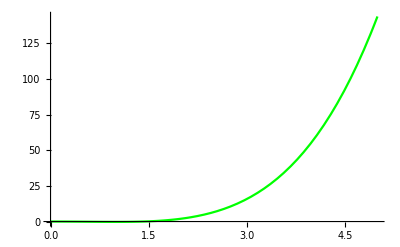

```mathematica
plot1 = Plot[Vx,{x,0,5}, PlotStyle->Green]
```

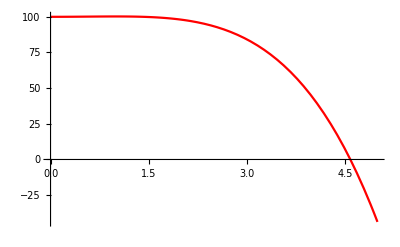

```mathematica
plot2 = Plot[Tx,{x,0,5},PlotStyle->Red]
```

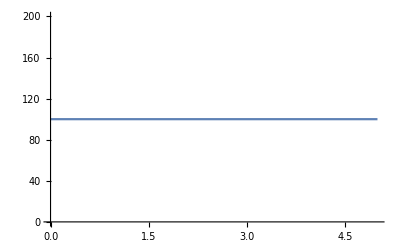

```mathematica
plot3 =Plot[Etot,{x,0,5}]
```

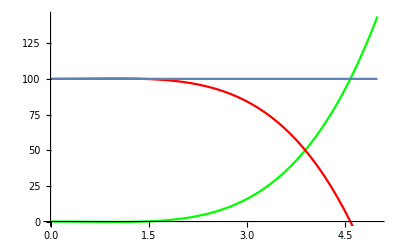

```mathematica
Show[plot1,plot2,plot3]
```

## Problem 2.9

A baseball of radius r =0.0366 m and mass .145 kg is dropped from rest from the top of the Empire State Building (height = 1250 Feet).  Calculate 
a) the initial potential energy of the baseball

```mathematica
r = 0.0366;
m = .145;
g = 9.8;
h = (1250*0.3048);
```

Potential energy is defined as V = m*g*x

```mathematica
V1 = m*g*h
```

541.401

b) The final kinetic energy 
Kinetic energy is equal to 1/2 m* v^2

```mathematica
c2 = 0.22(2*(0.0366))^2
```

0.00117881

```mathematica
T1 = 1/2*m((m*g)/c2)
```

87.3951

c) The total energy dissipated by the falling baseball.

```mathematica
Etotal = V1-T1
```

454.006

## Problem 2.12

A gun is fired straight up.  Assuming that the air drag on the bullet varies quadratically with speed, show that speed varies with height according to the equations

v^2= A*E^(-2kx)-g/k

v^2=g/k-B*E^(2kx)

In which A and B are constants of integration, g s the acceleration of gravity, and k = -c2/m where c2 is the drag constant and m is the mass of the bullet.

When we are going up

```mathematica
Clear[a]
```

```mathematica
Fnet= Fg +Fd
```

```mathematica
ay*m = -m*g+(-c2*v^2)
```

```mathematica
ay = -g-(c2*v^2)/m
```

```mathematica
ⅆvy/ⅆt= -g-(c2*v^2)/m
```

```mathematica
k =  c2/m
```

c2/m

```mathematica
Clear[k]
```

```mathematica
ⅆvy/ⅆy*ⅆy/ⅆt= -g-k*v^2
```

```mathematica
ⅆvy/ⅆy*vy = -g-k*v^2
```

```mathematica
∫_v0^vy (ⅆv*v)/(-g-k*v^2)=∫_0^y ⅆy
```

```mathematica
Integrate[v/(-g-k*v^2),v]
```

-Log[g+k v^2]/(2 k)

```mathematica
(-Log[g+k v^2]/(2 k)|)_v0^vy= y
```

```mathematica
(g+k*vy^2)/(g+k*v0^2)=E^(-2k*x)
```

```mathematica
Solve[(g+k*vy^2)/(g+k*v0^2)==E^(-2k*y),vy]
```

{{vy→-(√(-g+ⅇ^(-2 k y) g+ⅇ^(-2 k y) k v0^2))/(√k)},{vy→(√(-g+ⅇ^(-2 k y) g+ⅇ^(-2 k y) k v0^2))/(√k)}}

```mathematica
vy^2= (g/k+v0^2)E^(-2kx)-g/k
```

When we are going down,

```mathematica
ay*m = -m*g+k*v^2
```

```mathematica
ⅆvy/ⅆt= -g-(c2*v^2)/m
```

```mathematica
∫_v0^vy (ⅆv*v)/(-g+k*v^2)=∫_0^y ⅆy
```

```mathematica
Integrate[v/(-g+k*v^2),v]
```

Log[-g+k v^2]/(2 k)

```mathematica
(Log[-g+k v^2]/(2 k)|)_0^vy=y-y0
```

```mathematica
Log[-g+k v^2]/(2 k)/.v->0
```

Log[-g]/(2 k)

```mathematica
Log[-g+k v^2]/(2 k)/.v->vy
```

Log[-g+k vy^2]/(2 k)

```mathematica
1-k/g v^2=E^(2k*y)E^(-2k*y)
```

```mathematica
v^2=g/k-(g/k E^(-2k*y))E^(2k*y)
```